## Setup of functions we will need

```mathematica
$Assumptions=j>k>0&&γ>1
```

j>k>0&&γ>1

```mathematica
S[z_,w_]:=Conjugate[z].w
```

```mathematica
J[z_]:= Conjugate[{{0,1},{-1,0}}.z]
```

```mathematica
NN[ϕ_,θ_]:= {Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}
```

```mathematica
SpinorN[{x_,y_,z_}]:=1/(√2){-(x-I y)/(√(1+z)),√(1+z)}
```

We write the Tγ along the z axis

```mathematica
Tγz[r_]=({{Cosh[r], γ Sinh[r], 0}, {- γ Sinh[r], Cosh[r], 0}, {0, 0, 1}})
```

{{Cosh[r],γ Sinh[r],0},{-γ Sinh[r],Cosh[r],0},{0,0,1}}

```mathematica
Tm1γz[r_]=({{Cosh[r], -1/γ Sinh[r], 0}, {1/γ Sinh[r], Cosh[r], 0}, {0, 0, 1}})
```

{{Cosh[r],-Sinh[r]/γ,0},{Sinh[r]/γ,Cosh[r],0},{0,0,1}}

## Boundary Data

Dihedral angles. Valid for j>k>0 no issues here

```mathematica
Reduce[-1<-k/(3j)<1&&j>k>0]
```

k>0&&j>k

Equilateral tetrahedron

```mathematica
θe=ArcCos[-1/3];
```

```mathematica
n1=NN[1,0]
n2=NN[0,θe]
n3=NN[2/3π,θe]
n4=NN[4/3π,θe]
```

{0,0,1}

{(2 √2)/3,0,-1/3}

{-(√2)/3,√(2/3),-1/3}

{-(√2)/3,-√(2/3),-1/3}

```mathematica
k n1 + k n2 + k n3 + k n4
```

{0,0,0}

Isosceles Tetrahedron

```mathematica
θ0=ArcCos[-k/(3j)];
```

```mathematica
nt1=NN[1,0]
nt2=NN[0,θ0]
nt3=NN[2/3π,θ0]
nt4=NN[4/3π,θ0]
```

{0,0,1}

{√(1-k^2/(9 j^2)),0,-k/(3 j)}

{-1/2 √(1-k^2/(9 j^2)),1/2 √3 √(1-k^2/(9 j^2)),-k/(3 j)}

{-1/2 √(1-k^2/(9 j^2)),-1/2 √3 √(1-k^2/(9 j^2)),-k/(3 j)}

```mathematica
k nt1 + j nt2 + j nt3 + j nt4
```

{0,0,0}

```mathematica
z={0,0,1}
```

{0,0,1}

We derive also the tilde frame vectors

we compute first the spinor ztilde and the frame vector for  the boundary data

```mathematica
zt1=SpinorN[nt1];
F1=Im[S[J[zt1],PauliMatrix[#].zt1]&/@Range[3]]//FullSimplify;
nF1=Re[S[J[zt1],PauliMatrix[#].zt1]&/@Range[3]]//FullSimplify;
```

```mathematica
zt2=SpinorN[nt2];
F2=Im[S[J[zt2],PauliMatrix[#].zt2]&/@Range[3]]//FullSimplify;
nF2=Re[S[J[zt2],PauliMatrix[#].zt2]&/@Range[3]]//FullSimplify;
```

```mathematica
zt3=SpinorN[nt3];
F3=Im[S[J[zt3],PauliMatrix[#].zt3]&/@Range[3]]//FullSimplify;
nF3=Re[S[J[zt3],PauliMatrix[#].zt3]&/@Range[3]]//FullSimplify;
```

```mathematica
zt4=SpinorN[nt4];
F4=Im[S[J[zt4],PauliMatrix[#].zt4]&/@Range[3]]//FullSimplify;
nF4=Re[S[J[zt4],PauliMatrix[#].zt4]&/@Range[3]]//FullSimplify;
```

```mathematica
z1=SpinorN[n1];
z2=SpinorN[n2];
z3=SpinorN[n3];
z4=SpinorN[n4];
```

## The solution for the group element

The first solution is characterized by

```mathematica
r1=ArcSinh[Sqrt[j^2-k^2]/(k Sqrt[(1+γ^2)]Sqrt[(1-(z.n2)^2)])];
```

```mathematica
ψ1 =ArcCos[Cosh[r1]/(√(Cosh[r1]^2+γ^2 Sinh[r1]^2))];
```

Explicit  check that the boosted orientation equations are satisfied

```mathematica
Rzψ=RotationMatrix[ψ1,z]//FullSimplify;
```

```mathematica
Tγh = Rzψ.Tγz[r1]//FullSimplify;
```

```mathematica
Tγh.(k n1)==k nt1//FullSimplify
```

True

```mathematica
Tγh.(k n2)==j nt2//FullSimplify
```

True

```mathematica
Tγh.(k n3)==j nt3//FullSimplify
```

True

```mathematica
Tγh.(k n4)==j nt4//FullSimplify
```

True

The second solution is characterized by

```mathematica
r2=-ArcSinh[Sqrt[(j^2-k^2)/(k^2(1+γ^2)(1-(z.n2)^2))]];
```

```mathematica
ψ2=-ArcCos[Cosh[r2]/(√(Cosh[r2]^2+γ^2 Sinh[r2]^2))];
```

```mathematica
Rzψ2=RotationMatrix[ψ2,z]//FullSimplify;
```

Explicit  check that the boosted orientation equations are satisfied

```mathematica
Tγh2 = Rzψ2.Tγz[r2]//FullSimplify;
```

```mathematica
Tγh2.(k n1)==k nt1//FullSimplify
```

True

```mathematica
Tγh2.(k n2)==j nt2//FullSimplify
```

True

```mathematica
Tγh2.(k n3)==j nt3//FullSimplify
```

True

```mathematica
Tγh2.(k n4)==j nt4//FullSimplify
```

True

## The Flag phase at the first critical point

We use the formula derived in the paper to compute αt-βt

```mathematica
atmbt2=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F2+I nF2).Rzψ.(Cross[z,n2]/Norm[Cross[z,n2]])]//FullSimplify
atmbt3=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F3+I nF3).Rzψ.(Cross[z,n3]/Norm[Cross[z,n3]])]//FullSimplify
atmbt4=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F4+I nF4).Rzψ.(Cross[z,n4]/Norm[Cross[z,n4]])]//FullSimplify
```

Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

Arg[(ⅈ+√3) (-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

Arg[(1+ⅈ √3) (j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

## Vectorial phase and norm factor at the first critical point

The ratio of the norms is obtained from

```mathematica
logzoverhz21=Log[Cosh[r1]- z.n1 Sinh[r1]]//Simplify
logzoverhz22=Log[Cosh[r1]- z.n2 Sinh[r1]]//Simplify
logzoverhz23=Log[Cosh[r1]- z.n3 Sinh[r1]]//Simplify
logzoverhz24=Log[Cosh[r1]- z.n4 Sinh[r1]]//Simplify
```

Log[(-3 √(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

Here we used that u\\n_1 to get simply

```mathematica
αmαtl1=-ψ1/2//FullSimplify
```

-1/2 ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]

```mathematica
υ[z2_]:=Arg[S[z2,SpinorN[z]]S[SpinorN[z],J[z2]]]
```

```mathematica
tαtmαmβ2= ArcTan[γ]+ υ[z2]+If[Sign[r1]>0,π,0]//FullSimplify
tαtmαmβ3= ArcTan[γ]+ υ[z3]+If[Sign[r1]>0,π,0]//FullSimplify
tαtmαmβ4= ArcTan[γ]+ υ[z4]+If[Sign[r1]>0,π,0]//FullSimplify
```

π+ArcTan[γ]

(5 π)/3+ArcTan[γ]

π/3+ArcTan[γ]

## Vectorial phase and norm factor at the second critical point

We use the formula derived in the paper to compute αt-βt

```mathematica
atmbt2b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F2+I nF2).Rzψ2.(Cross[z,n2]/Norm[Cross[z,n2]])]//FullSimplify
atmbt3b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F3+I nF3).Rzψ2.(Cross[z,n3]/Norm[Cross[z,n3]])]//FullSimplify
atmbt4b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F4+I nF4).Rzψ2.(Cross[z,n4]/Norm[Cross[z,n4]])]//FullSimplify
```

Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

Arg[ⅈ (ⅈ+√3) (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

Arg[(-ⅈ+√3) (-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]

The ratio of the norms is obtained from

```mathematica
logzoverhz21b=Log[Cosh[r2]- z.n1 Sinh[r2]]//Simplify
logzoverhz22b=Log[Cosh[r2]- z.n2 Sinh[r2]]//Simplify
logzoverhz23b=Log[Cosh[r2]- z.n3 Sinh[r2]]//Simplify
logzoverhz24b=Log[Cosh[r2]- z.n4 Sinh[r2]]//Simplify
```

Log[(3 √((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

Here we used that u\\n_1 to get simply

```mathematica
αmαtl1b=-ψ2/2//FullSimplify
```

1/2 ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]

```mathematica
tαtmαmβ2b= ArcTan[γ]+ υ[z2]+If[Sign[r2]>0,π,0]//FullSimplify
tαtmαmβ3b= ArcTan[γ]+ υ[z3]+If[Sign[r2]>0,π,0]//FullSimplify
tαtmαmβ4b= ArcTan[γ]+ υ[z4]+If[Sign[r2]>0,π,0]//FullSimplify
```

ArcTan[γ]

(2 π)/3+ArcTan[γ]

-(2 π)/3+ArcTan[γ]

## Action at the critical points

We focus on the first critical point

lowest spins strand

```mathematica
strand1S=-2 k I αmαtl1 + I γ k logzoverhz21
```

ⅈ k ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]+ⅈ k γ Log[(-3 √(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

half-lowest spins strands. I am omitting the real part of the action!

```mathematica
strand2S=- I k tαtmαmβ2 + I j atmbt2 +  I γ k logzoverhz22
strand3S= - I k tαtmαmβ3 + I j atmbt3 +  I γ k logzoverhz23
strand4S= - I k tαtmαmβ4 + I j atmbt4+  I γ k logzoverhz24
```

-ⅈ k (π+ArcTan[γ])+ⅈ j Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

-ⅈ k ((5 π)/3+ArcTan[γ])+ⅈ j Arg[(ⅈ+√3) (-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

-ⅈ k (π/3+ArcTan[γ])+ⅈ j Arg[(1+ⅈ √3) (j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

```mathematica
Action1 = strand1S+strand2S+strand3S+strand4S
```

ⅈ k ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]-ⅈ k (π/3+ArcTan[γ])-ⅈ k (π+ArcTan[γ])-ⅈ k ((5 π)/3+ArcTan[γ])+ⅈ j Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ j Arg[(1+ⅈ √3) (j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ j Arg[(ⅈ+√3) (-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[(-3 √(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]+3 ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(9 j^2)/k^2+8 γ^2))/(2 √2 k √(1+γ^2))]

At the second critical point

lowest spins strand

```mathematica
strand1Sb=-2 k I αmαtl1b + I γ k logzoverhz21b
```

-ⅈ k ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]+ⅈ k γ Log[(3 √((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

half-lowest spins strands. I am omitting the real part of the action!

```mathematica
strand2Sb=- I k tαtmαmβ2b + I j atmbt2b +  I γ k logzoverhz22b
strand3Sb= - I k tαtmαmβ3b + I j atmbt3b +  I γ k logzoverhz23b
strand4Sb= - I k tαtmαmβ4b + I j atmbt4b+  I γ k logzoverhz24b
```

-ⅈ k ArcTan[γ]+ⅈ j Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

-ⅈ k ((2 π)/3+ArcTan[γ])+ⅈ j Arg[ⅈ (ⅈ+√3) (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

-ⅈ k (-(2 π)/3+ArcTan[γ])+ⅈ j Arg[(-ⅈ+√3) (-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

```mathematica
Action2 = strand1Sb+strand2Sb+strand3Sb+strand4Sb
```

-ⅈ k ArcSec[√(((9 j^2-k^2) (1+γ^2))/(9 j^2+k^2 (-1+8 γ^2)))]-ⅈ k ArcTan[γ]-ⅈ k (-(2 π)/3+ArcTan[γ])-ⅈ k ((2 π)/3+ArcTan[γ])+ⅈ j Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ j Arg[ⅈ (ⅈ+√3) (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+ⅈ j Arg[(-ⅈ+√3) (-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(9 j^2+k^2 (-1+8 γ^2))))]+3 ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]+ⅈ k γ Log[(3 √((j^2-k^2)/(1+γ^2)))/(2 √2 k)+√(1+(9 (j^2-k^2))/(8 k^2 (1+γ^2)))]

The difference of the two actions at the critical points is given by

```mathematica
Mod[N[(Action1-Action2)/.{γ->6/5,j-> 2,k->1}],2π]
```

0.+2.27627 ⅈ

remember that these are all phases defined up to 2π

## Numerical data for the coherent invariant with j=2 k=1 γ=6/5 with λ=1, ... , 80

```mathematica
data={{1,0.000162718-2.33421*^-21 ⅈ},{2,-0.0000430947+1.95073*^-22 ⅈ},{3,-0.0000110155-7.41464*^-23 ⅈ},{4,-2.47856*^-7+1.01329*^-23 ⅈ},{5,1.60352*^-6-1.54107*^-23 ⅈ},{6,7.11296*^-7-1.33343*^-24 ⅈ},{7,-2.41968*^-8+1.32815*^-24 ⅈ},{8,-2.82668*^-7-8.16124*^-25 ⅈ},{9,-1.64712*^-7-1.34393*^-24 ⅈ},{10,4.01654*^-8-1.7249*^-25 ⅈ},{11,1.01872*^-7+3.51337*^-25 ⅈ},{12,3.96552*^-8-1.01468*^-25 ⅈ},{13,-2.80266*^-8-3.66254*^-26 ⅈ},{14,-3.9563*^-8-1.36295*^-25 ⅈ},{15,-1.16207*^-8-5.93242*^-26 ⅈ},{16,1.74017*^-8-1.19808*^-25 ⅈ},{17,1.92487*^-8+8.22219*^-26 ⅈ},{18,1.53336*^-9-1.11982*^-26 ⅈ},{19,-1.1621*^-8-1.85201*^-26 ⅈ},{20,-8.86156*^-9+2.72796*^-26 ⅈ},{21,1.45223*^-9-6.6245*^-27 ⅈ},{22,7.32358*^-9+1.97671*^-26 ⅈ},{23,4.31298*^-9+2.84092*^-26 ⅈ},{24,-2.28682*^-9+4.27301*^-27 ⅈ},{25,-4.83687*^-9+8.60523*^-27 ⅈ},{26,-1.74326*^-9+7.87457*^-27 ⅈ},{27,2.30759*^-9+4.65726*^-27 ⅈ},{28,2.99837*^-9+6.08425*^-27 ⅈ},{29,4.91345*^-10+2.76767*^-27 ⅈ},{30,-1.97007*^-9-5.39158*^-27 ⅈ},{31,-1.8672*^-9-1.01302*^-27 ⅈ},{32,1.75785*^-10+2.65018*^-28 ⅈ},{33,1.60849*^-9+8.44489*^-27 ⅈ},{34,1.05297*^-9+2.53673*^-27 ⅈ},{35,-4.83491*^-10-2.83273*^-27 ⅈ},{36,-1.2144*^-9-5.87052*^-27 ⅈ},{37,-5.38039*^-10-5.41637*^-28 ⅈ},{38,5.87932*^-10-3.63507*^-28 ⅈ},{39,8.94381*^-10+2.39563*^-27 ⅈ},{40,1.90747*^-10+3.38752*^-28 ⅈ},{41,-5.93655*^-10-7.12867*^-28 ⅈ},{42,-6.10611*^-10-2.95734*^-27 ⅈ},{43,2.32391*^-11+2.99487*^-28 ⅈ},{44,5.30794*^-10+1.14158*^-27 ⅈ},{45,3.9336*^-10+4.3039*^-28 ⅈ},{46,-1.47651*^-10-9.40194*^-28 ⅈ},{47,-4.49555*^-10-2.61771*^-27 ⅈ},{48,-2.20321*^-10-6.18285*^-28 ⅈ},{49,2.12404*^-10+7.6041*^-28 ⅈ},{50,3.53182*^-10+2.06413*^-27 ⅈ},{51,9.40334*^-11+2.02393*^-28 ⅈ},{52,-2.31862*^-10-6.12821*^-28 ⅈ},{53,-2.6377*^-10-5.75893*^-28 ⅈ},{54,-3.94022*^-12+2.35708*^-30 ⅈ},{55,2.26657*^-10+8.70655*^-28 ⅈ},{56,1.80226*^-10+8.7257*^-28 ⅈ},{57,-5.61637*^-11-1.60925*^-28 ⅈ},{58,-2.01839*^-10-1.05079*^-27 ⅈ},{59,-1.10244*^-10-2.80829*^-28 ⅈ},{60,9.12271*^-11+4.08276*^-28 ⅈ},{61,1.69654*^-10-1.51091*^-28 ⅈ},{62,5.26866*^-11+2.4131*^-28 ⅈ},{63,-1.08652*^-10-3.20128*^-28 ⅈ},{64,-1.3231*^-10-5.15147*^-28 ⅈ},{65,-8.43591*^-12-3.81185*^-29 ⅈ},{66,1.11166*^-10+4.04359*^-28 ⅈ},{67,9.60165*^-11-2.38223*^-29 ⅈ},{68,-2.34206*^-11-8.71418*^-30 ⅈ},{69,-1.04726*^-10-2.21245*^-28 ⅈ},{70,-6.19571*^-11-2.94006*^-28 ⅈ},{71,4.47155*^-11+1.267*^-28 ⅈ},{72,9.11946*^-11+2.30768*^-28 ⅈ},{73,3.25422*^-11+1.71995*^-28 ⅈ},{74,-5.63819*^-11-2.25822*^-28 ⅈ},{75,-7.45264*^-11-2.2344*^-28 ⅈ},{76,-8.33344*^-12-3.45821*^-29 ⅈ},{77,6.08949*^-11+2.09333*^-28 ⅈ},{78,5.60977*^-11+2.25833*^-28 ⅈ},{79,-1.0378*^-11-7.35106*^-29 ⅈ},{80,-5.92743*^-11-3.27431*^-28 ⅈ}};
```

```mathematica
listplot = ListLogLogPlot[Abs[data],PlotStyle->Darker[Red],PlotMarkers->{Automatic,14},ImageSize->1000,Ticks->{All,All},PlotRange->All,AxesLabel->{"λ","|I|"},LabelStyle->Directive[24,Black]];
powerlaw = LogLogPlot[ 10^-3*λ^(-15/4),{λ,1,80},PlotStyle->{Thickness[.004],Blue}];
```

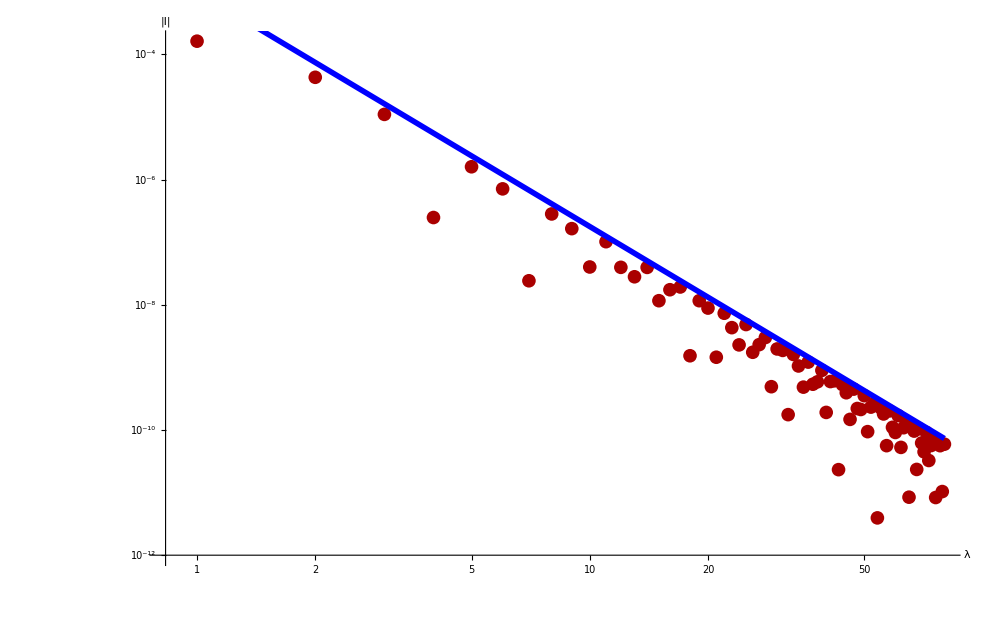

```mathematica
Show[listplot,powerlaw]
```